Initialize:

```mathematica
Clear[Ωp,Ωs]
```

The coupling of three states in the lambda configuration by two lasers is given by the following Hamiltonian.

```mathematica
H[t_]=({{0, Ωp[t], 0}, {Ωp[t], 2Δp, Ωs[t]}, {0, Ωs[t], 2(Δp-Δs)}});
```

We find the eigenstates and eigen-energies of the system for a two photon resonance.

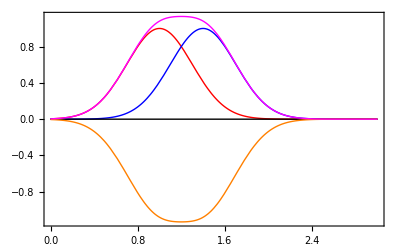
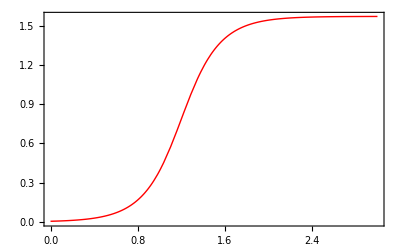
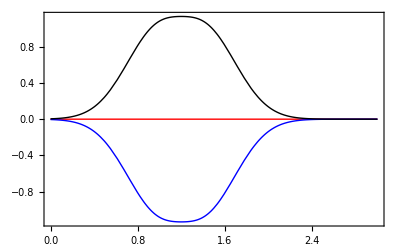

```mathematica
{Hvals,Hvecs}=Eigensystem[H[t]/.{Δp->Δ,Δs->Δ}];
Hvecs=ComplexExpand[Normalize/@Hvecs];
Ωs[t_]=Exp[-(t-1)^2/(2 (.3)^2)];
Ωp[t_]=Exp[-(t-1.4)^2/(2 (.3)^2)];
plotΩ=Plot[{Ωs[t],Ωp[t],Evaluate[Hvals/.Δ->0]},{t,0,3}];
plotΘ=Plot[ArcTan[Ωp[t]/Ωs[t]],{t,0,3},Ticks->{Automatic,Range[0,Pi/2,Pi/4]}];
plotω=Plot[Evaluate[Hvals/.Δ->0],{t,0,3},PlotRange->All];
({{plotΩ, plotΘ, plotω}})
```

```mathematica
Show[Graphics3D[{Blue,Arrow[Tube[{{0,0,0},{1,1,1}}]]},Axes->True,AxesLabel->{1,2,3}]]
```

-Graphics3D-